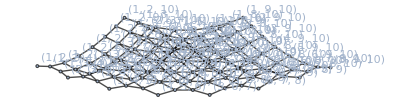

```mathematica
g=Import["C:\\Users\\Joel9\\Documents\\Investigacion Grafos\\Packing and 3token graphs\\Archivos Pn\\P10\\F3.gml"]
```

```mathematica
VertexList[g]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119}

```mathematica
m=TableForm[GraphDistanceMatrix[g],TableHeadings->{c=Style[#,Red]&/@%,c}]
```

| 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119
0 | 0 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 9 | 10 | 10 | 11 | 11 | 12 | 12 | 11 | 12 | 12 | 13 | 13 | 13 | 14 | 14 | 15 | 6 | 7 | 8 | 9 | 10 | 11 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 9 | 10 | 11 | 12 | 13 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 12 | 13 | 14 | 15 | 14 | 15 | 16 | 16 | 17 | 18 | 15 | 16 | 17 | 17 | 18 | 19 | 18 | 19 | 20 | 21
1 | 1 | 0 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 8 | 9 | 9 | 10 | 10 | 11 | 11 | 10 | 11 | 11 | 12 | 12 | 12 | 13 | 13 | 14 | 5 | 6 | 7 | 8 | 9 | 10 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 8 | 9 | 10 | 11 | 12 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 11 | 12 | 13 | 14 | 13 | 14 | 15 | 15 | 16 | 17 | 14 | 15 | 16 | 16 | 17 | 18 | 17 | 18 | 19 | 20
2 | 2 | 1 | 0 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 9 | 10 | 10 | 11 | 11 | 11 | 12 | 12 | 13 | 4 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 13 | 14 | 15 | 15 | 16 | 17 | 16 | 17 | 18 | 19
3 | 2 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 6 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 9 | 10 | 10 | 11 | 11 | 11 | 12 | 12 | 13 | 4 | 5 | 6 | 7 | 8 | 9 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 7 | 8 | 9 | 10 | 11 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 10 | 11 | 12 | 13 | 12 | 13 | 14 | 14 | 15 | 16 | 13 | 14 | 15 | 15 | 16 | 17 | 16 | 17 | 18 | 19
4 | 3 | 2 | 1 | 3 | 0 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 8 | 9 | 9 | 10 | 10 | 10 | 11 | 11 | 12 | 5 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 12 | 13 | 14 | 14 | 15 | 16 | 15 | 16 | 17 | 18
5 | 3 | 2 | 1 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 5 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 8 | 9 | 9 | 10 | 10 | 10 | 11 | 11 | 12 | 3 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 12 | 13 | 14 | 14 | 15 | 16 | 15 | 16 | 17 | 18
6 | 4 | 3 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 7 | 8 | 8 | 9 | 9 | 9 | 10 | 10 | 11 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 11 | 12 | 13 | 13 | 14 | 15 | 14 | 15 | 16 | 17
7 | 4 | 3 | 2 | 2 | 1 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 4 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 7 | 8 | 8 | 9 | 9 | 9 | 10 | 10 | 11 | 4 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 11 | 12 | 13 | 13 | 14 | 15 | 14 | 15 | 16 | 17
8 | 5 | 4 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 1 | 2 | 2 | 3 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 6 | 7 | 7 | 8 | 8 | 8 | 9 | 9 | 10 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 7 | 6 | 7 | 8 | 8 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 11 | 12 | 12 | 13 | 14 | 13 | 14 | 15 | 16
9 | 5 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 3 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 6 | 7 | 7 | 8 | 8 | 8 | 9 | 9 | 10 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 11 | 12 | 12 | 13 | 14 | 13 | 14 | 15 | 16
10 | 6 | 5 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 1 | 2 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 6 | 6 | 7 | 7 | 7 | 8 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 7 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 7 | 9 | 8 | 7 | 8 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 9 | 8 | 9 | 10 | 9 | 10 | 10 | 11 | 12 | 11 | 10 | 11 | 11 | 12 | 13 | 12 | 13 | 14 | 15
11 | 6 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 0 | 3 | 1 | 2 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 5 | 6 | 6 | 7 | 7 | 7 | 8 | 8 | 9 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 6 | 5 | 6 | 7 | 7 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 10 | 11 | 11 | 12 | 13 | 12 | 13 | 14 | 15
12 | 7 | 6 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 8 | 7 | 7 | 6 | 6 | 8 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 4 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 8 | 7 | 6 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 11 | 10 | 11 | 12 | 11 | 10 | 12 | 11 | 12 | 13 | 12 | 13 | 14
13 | 7 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 0 | 1 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 5 | 5 | 6 | 6 | 6 | 7 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 4 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 6 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 6 | 8 | 7 | 6 | 7 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 7 | 8 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 9 | 10 | 10 | 11 | 12 | 11 | 12 | 13 | 14
14 | 8 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 0 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 7 | 6 | 6 | 5 | 5 | 7 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 3 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 5 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 9 | 11 | 10 | 11 | 12 | 11 | 12 | 13
15 | 3 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 7 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 6 | 9 | 7 | 10 | 8 | 11 | 9 | 8 | 11 | 9 | 12 | 10 | 10 | 13 | 11 | 12 | 3 | 4 | 5 | 6 | 7 | 8 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 6 | 7 | 8 | 9 | 10 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 9 | 10 | 11 | 12 | 11 | 12 | 13 | 13 | 14 | 15 | 12 | 13 | 14 | 14 | 15 | 16 | 15 | 16 | 17 | 18
16 | 4 | 3 | 2 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 6 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 7 | 8 | 8 | 9 | 9 | 9 | 10 | 10 | 11 | 2 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 11 | 12 | 13 | 13 | 14 | 15 | 14 | 15 | 16 | 17
17 | 4 | 3 | 2 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 6 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 7 | 10 | 8 | 11 | 9 | 9 | 12 | 10 | 11 | 2 | 3 | 4 | 5 | 6 | 7 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 5 | 6 | 7 | 8 | 9 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 8 | 9 | 10 | 11 | 10 | 11 | 12 | 12 | 13 | 14 | 11 | 12 | 13 | 13 | 14 | 15 | 14 | 15 | 16 | 17
18 | 5 | 4 | 3 | 3 | 2 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 5 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 6 | 7 | 7 | 8 | 8 | 8 | 9 | 9 | 10 | 3 | 2 | 3 | 4 | 5 | 6 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 11 | 12 | 12 | 13 | 14 | 13 | 14 | 15 | 16
19 | 5 | 4 | 3 | 3 | 2 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 5 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 6 | 9 | 7 | 10 | 8 | 8 | 11 | 9 | 10 | 3 | 2 | 3 | 4 | 5 | 6 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 11 | 12 | 12 | 13 | 14 | 13 | 14 | 15 | 16
20 | 6 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 4 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 5 | 6 | 6 | 7 | 7 | 7 | 8 | 8 | 9 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 5 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 10 | 11 | 11 | 12 | 13 | 12 | 13 | 14 | 15
21 | 6 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 4 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 5 | 8 | 6 | 9 | 7 | 7 | 10 | 8 | 9 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 5 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 10 | 11 | 11 | 12 | 13 | 12 | 13 | 14 | 15
22 | 7 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 1 | 4 | 2 | 3 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 4 | 5 | 5 | 6 | 6 | 6 | 7 | 7 | 8 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 9 | 10 | 10 | 11 | 12 | 11 | 12 | 13 | 14
23 | 7 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 1 | 4 | 2 | 3 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 4 | 7 | 5 | 8 | 6 | 6 | 9 | 7 | 8 | 5 | 4 | 3 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 5 | 4 | 5 | 6 | 6 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 9 | 10 | 10 | 11 | 12 | 11 | 12 | 13 | 14
24 | 8 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 1 | 2 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 4 | 4 | 5 | 5 | 5 | 6 | 6 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 6 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 11 | 12 | 13
25 | 8 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 1 | 2 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 5 | 6 | 4 | 7 | 5 | 5 | 8 | 6 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 7 | 6 | 5 | 6 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 8 | 9 | 9 | 10 | 11 | 10 | 11 | 12 | 13
26 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 6 | 5 | 5 | 4 | 4 | 6 | 5 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 2 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 11 | 12
27 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 6 | 7 | 5 | 6 | 4 | 6 | 7 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 2 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 8 | 10 | 9 | 10 | 11 | 10 | 11 | 12
28 | 5 | 4 | 3 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 7 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 6 | 9 | 7 | 10 | 8 | 8 | 11 | 9 | 10 | 1 | 2 | 3 | 4 | 5 | 6 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 4 | 5 | 6 | 7 | 8 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 7 | 8 | 9 | 10 | 9 | 10 | 11 | 11 | 12 | 13 | 10 | 11 | 12 | 12 | 13 | 14 | 13 | 14 | 15 | 16
29 | 6 | 5 | 4 | 4 | 3 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 6 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 5 | 6 | 6 | 7 | 7 | 7 | 8 | 8 | 9 | 4 | 3 | 4 | 5 | 6 | 7 | 2 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 10 | 11 | 11 | 12 | 13 | 12 | 13 | 14 | 15
30 | 6 | 5 | 4 | 4 | 3 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 6 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 5 | 8 | 6 | 9 | 7 | 7 | 10 | 8 | 9 | 2 | 1 | 2 | 3 | 4 | 5 | 2 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 10 | 11 | 11 | 12 | 13 | 12 | 13 | 14 | 15
31 | 7 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 5 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 4 | 5 | 5 | 6 | 6 | 6 | 7 | 7 | 8 | 5 | 4 | 3 | 4 | 5 | 6 | 3 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 4 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 9 | 10 | 10 | 11 | 12 | 11 | 12 | 13 | 14
32 | 7 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 5 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 4 | 7 | 5 | 8 | 6 | 6 | 9 | 7 | 8 | 3 | 2 | 1 | 2 | 3 | 4 | 3 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 4 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 9 | 10 | 10 | 11 | 12 | 11 | 12 | 13 | 14
33 | 8 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 2 | 5 | 3 | 4 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 3 | 4 | 4 | 5 | 5 | 5 | 6 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 8 | 9 | 9 | 10 | 11 | 10 | 11 | 12 | 13
34 | 8 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 2 | 5 | 3 | 4 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 3 | 6 | 4 | 7 | 5 | 5 | 8 | 6 | 7 | 4 | 3 | 2 | 1 | 2 | 3 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 5 | 4 | 3 | 4 | 5 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 8 | 9 | 9 | 10 | 11 | 10 | 11 | 12 | 13
35 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 2 | 3 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 3 | 3 | 4 | 4 | 4 | 5 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 10 | 11 | 12
36 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 2 | 3 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 4 | 5 | 3 | 6 | 4 | 4 | 7 | 5 | 6 | 5 | 4 | 3 | 2 | 1 | 2 | 5 | 4 | 3 | 2 | 3 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 7 | 8 | 8 | 9 | 10 | 9 | 10 | 11 | 12
37 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 5 | 4 | 4 | 3 | 3 | 5 | 4 | 4 | 5 | 8 | 7 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 3 | 2 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 10 | 11
38 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 6 | 4 | 5 | 3 | 5 | 6 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 1 | 6 | 5 | 4 | 3 | 2 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 7 | 9 | 8 | 9 | 10 | 9 | 10 | 11
39 | 7 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 7 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 4 | 7 | 5 | 8 | 6 | 6 | 9 | 7 | 8 | 3 | 2 | 3 | 4 | 5 | 6 | 1 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 2 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 9 | 10 | 10 | 11 | 12 | 11 | 12 | 13 | 14
40 | 8 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 6 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 6 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 3 | 5 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 3 | 4 | 4 | 5 | 5 | 5 | 6 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 7 | 4 | 3 | 4 | 5 | 6 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 5 | 4 | 5 | 6 | 7 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 8 | 9 | 9 | 10 | 11 | 10 | 11 | 12 | 13
41 | 8 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 6 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 3 | 6 | 4 | 7 | 5 | 5 | 8 | 6 | 7 | 4 | 3 | 2 | 3 | 4 | 5 | 2 | 1 | 2 | 3 | 4 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 3 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 8 | 9 | 9 | 10 | 11 | 10 | 11 | 12 | 13
42 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 5 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 4 | 6 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 2 | 3 | 3 | 4 | 4 | 4 | 5 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 3 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 7 | 8 | 8 | 9 | 10 | 9 | 10 | 11 | 12
43 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 5 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 2 | 5 | 3 | 6 | 4 | 4 | 7 | 5 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 3 | 3 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 7 | 8 | 8 | 9 | 10 | 9 | 10 | 11 | 12
44 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 4 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 2 | 2 | 3 | 3 | 3 | 4 | 4 | 5 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 4 | 3 | 2 | 3 | 4 | 3 | 4 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 9 | 10 | 11
45 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 4 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 3 | 4 | 2 | 5 | 3 | 3 | 6 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 4 | 3 | 2 | 3 | 4 | 3 | 4 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 3 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 9 | 10 | 11
46 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 4 | 3 | 3 | 2 | 2 | 4 | 3 | 3 | 4 | 9 | 8 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 4 | 3 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 9 | 10
47 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 5 | 3 | 4 | 2 | 4 | 5 | 3 | 4 | 7 | 6 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 2 | 1 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 9 | 10
48 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 7 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 0 | 3 | 1 | 4 | 2 | 5 | 3 | 2 | 5 | 3 | 6 | 4 | 4 | 7 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 6 | 3 | 2 | 3 | 4 | 5 | 1 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 4 | 3 | 4 | 5 | 6 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 7 | 8 | 8 | 9 | 10 | 9 | 10 | 11 | 12
49 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 7 | 5 | 6 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 4 | 6 | 5 | 7 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 4 | 6 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 5 | 3 | 0 | 2 | 1 | 3 | 2 | 4 | 1 | 2 | 2 | 3 | 3 | 3 | 4 | 4 | 5 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 4 | 3 | 4 | 5 | 2 | 3 | 4 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 5 | 4 | 5 | 6 | 3 | 4 | 5 | 5 | 6 | 7 | 6 | 5 | 6 | 7 | 4 | 5 | 6 | 6 | 7 | 8 | 5 | 6 | 7 | 7 | 8 | 9 | 8 | 9 | 10 | 11
50 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 7 | 5 | 6 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 1 | 2 | 0 | 3 | 1 | 4 | 2 | 1 | 4 | 2 | 5 | 3 | 3 | 6 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 2 | 1 | 2 | 3 | 2 | 3 | 4 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 3 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 5 | 6 | 7 | 7 | 8 | 9 | 8 | 9 | 10 | 11
51 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 5 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 4 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 4 | 1 | 3 | 0 | 2 | 1 | 3 | 2 | 1 | 1 | 2 | 2 | 2 | 3 | 3 | 4 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 3 | 2 | 3 | 3 | 4 | 5 | 8 | 7 | 6 | 5 | 6 | 6 | 5 | 4 | 5 | 4 | 3 | 4 | 4 | 5 | 6 | 7 | 6 | 5 | 6 | 5 | 4 | 5 | 5 | 6 | 7 | 6 | 5 | 6 | 6 | 7 | 8 | 7 | 8 | 9 | 10
52 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 5 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 2 | 3 | 1 | 2 | 0 | 3 | 1 | 2 | 3 | 1 | 4 | 2 | 2 | 5 | 3 | 4 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 3 | 2 | 1 | 2 | 3 | 2 | 3 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 4 | 3 | 2 | 3 | 4 | 3 | 4 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 6 | 5 | 6 | 6 | 7 | 8 | 7 | 8 | 9 | 10
53 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 5 | 2 | 4 | 1 | 3 | 0 | 2 | 3 | 2 | 2 | 1 | 1 | 3 | 2 | 2 | 3 | 10 | 9 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 4 | 3 | 4 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 6 | 5 | 4 | 6 | 5 | 6 | 7 | 6 | 5 | 7 | 6 | 7 | 8 | 7 | 8 | 9
54 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 3 | 4 | 2 | 3 | 1 | 2 | 0 | 3 | 4 | 2 | 3 | 1 | 3 | 4 | 2 | 3 | 8 | 7 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 3 | 2 | 4 | 3 | 2 | 1 | 4 | 3 | 2 | 4 | 3 | 4 | 7 | 6 | 5 | 4 | 3 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 7 | 6 | 5 | 7 | 6 | 7 | 8 | 7 | 8 | 9
55 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 8 | 6 | 7 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 2 | 1 | 1 | 2 | 2 | 3 | 3 | 0 | 3 | 1 | 4 | 2 | 2 | 5 | 3 | 4 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 3 | 2 | 3 | 4 | 1 | 2 | 3 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 4 | 3 | 4 | 5 | 2 | 3 | 4 | 4 | 5 | 6 | 5 | 4 | 5 | 6 | 3 | 4 | 5 | 5 | 6 | 7 | 4 | 5 | 6 | 6 | 7 | 8 | 7 | 8 | 9 | 10
56 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 6 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 5 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 4 | 6 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 3 | 5 | 5 | 2 | 4 | 1 | 3 | 2 | 4 | 3 | 0 | 2 | 1 | 3 | 1 | 2 | 2 | 3 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 6 | 5 | 4 | 5 | 4 | 3 | 4 | 2 | 3 | 4 | 9 | 8 | 7 | 6 | 7 | 7 | 6 | 5 | 6 | 5 | 4 | 5 | 3 | 4 | 5 | 8 | 7 | 6 | 7 | 6 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 5 | 6 | 7 | 6 | 7 | 8 | 9
57 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 6 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 2 | 1 | 2 | 0 | 3 | 1 | 1 | 4 | 2 | 3 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 4 | 3 | 2 | 3 | 2 | 1 | 2 | 2 | 3 | 4 | 7 | 6 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 3 | 2 | 3 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 4 | 3 | 4 | 4 | 5 | 6 | 5 | 4 | 5 | 5 | 6 | 7 | 6 | 7 | 8 | 9
58 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 6 | 3 | 5 | 2 | 4 | 1 | 3 | 4 | 1 | 3 | 0 | 2 | 2 | 1 | 1 | 2 | 11 | 10 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 3 | 2 | 3 | 10 | 9 | 8 | 7 | 6 | 8 | 7 | 6 | 5 | 6 | 5 | 4 | 4 | 3 | 4 | 9 | 8 | 7 | 6 | 7 | 6 | 5 | 5 | 4 | 5 | 8 | 7 | 6 | 6 | 5 | 6 | 7 | 6 | 7 | 8
59 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 4 | 3 | 3 | 2 | 2 | 1 | 1 | 2 | 3 | 1 | 2 | 0 | 2 | 3 | 1 | 2 | 9 | 8 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 4 | 3 | 5 | 4 | 3 | 2 | 3 | 2 | 1 | 3 | 2 | 3 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 4 | 3 | 4 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 5 | 4 | 5 | 6 | 5 | 4 | 6 | 5 | 6 | 7 | 6 | 7 | 8
60 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 6 | 7 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 1 | 1 | 2 | 2 | 0 | 3 | 1 | 2 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 3 | 2 | 3 | 1 | 2 | 3 | 8 | 7 | 6 | 5 | 6 | 6 | 5 | 4 | 5 | 4 | 3 | 4 | 2 | 3 | 4 | 7 | 6 | 5 | 6 | 5 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 4 | 5 | 6 | 5 | 6 | 7 | 8
61 | 14 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 13 | 10 | 12 | 9 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 11 | 8 | 10 | 7 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 9 | 6 | 8 | 5 | 7 | 4 | 6 | 3 | 5 | 7 | 4 | 6 | 3 | 5 | 2 | 4 | 5 | 2 | 4 | 1 | 3 | 3 | 0 | 2 | 1 | 12 | 11 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 7 | 6 | 8 | 7 | 6 | 5 | 6 | 5 | 4 | 4 | 3 | 2 | 11 | 10 | 9 | 8 | 7 | 9 | 8 | 7 | 6 | 7 | 6 | 5 | 5 | 4 | 3 | 10 | 9 | 8 | 7 | 8 | 7 | 6 | 6 | 5 | 4 | 9 | 8 | 7 | 7 | 6 | 5 | 8 | 7 | 6 | 7
62 | 14 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 2 | 2 | 1 | 1 | 1 | 2 | 0 | 1 | 10 | 9 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 2 | 1 | 2 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 3 | 2 | 3 | 8 | 7 | 6 | 5 | 6 | 5 | 4 | 4 | 3 | 4 | 7 | 6 | 5 | 5 | 4 | 5 | 6 | 5 | 6 | 7
63 | 15 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 3 | 3 | 2 | 2 | 2 | 1 | 1 | 0 | 11 | 10 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 3 | 2 | 1 | 10 | 9 | 8 | 7 | 6 | 8 | 7 | 6 | 5 | 6 | 5 | 4 | 4 | 3 | 2 | 9 | 8 | 7 | 6 | 7 | 6 | 5 | 5 | 4 | 3 | 8 | 7 | 6 | 6 | 5 | 4 | 7 | 6 | 5 | 6
64 | 6 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 8 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 7 | 10 | 8 | 11 | 9 | 9 | 12 | 10 | 11 | 0 | 1 | 2 | 3 | 4 | 5 | 2 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 3 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 6 | 7 | 8 | 9 | 8 | 9 | 10 | 10 | 11 | 12 | 9 | 10 | 11 | 11 | 12 | 13 | 12 | 13 | 14 | 15
65 | 7 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 7 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 6 | 9 | 7 | 10 | 8 | 8 | 11 | 9 | 10 | 1 | 0 | 1 | 2 | 3 | 4 | 1 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 2 | 3 | 4 | 5 | 6 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 5 | 6 | 7 | 8 | 7 | 8 | 9 | 9 | 10 | 11 | 8 | 9 | 10 | 10 | 11 | 12 | 11 | 12 | 13 | 14
66 | 8 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 6 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 5 | 8 | 6 | 9 | 7 | 7 | 10 | 8 | 9 | 2 | 1 | 0 | 1 | 2 | 3 | 2 | 1 | 2 | 3 | 4 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 3 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 8 | 9 | 9 | 10 | 11 | 10 | 11 | 12 | 13
67 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 6 | 4 | 5 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 4 | 7 | 5 | 8 | 6 | 6 | 9 | 7 | 8 | 3 | 2 | 1 | 0 | 1 | 2 | 3 | 2 | 1 | 2 | 3 | 3 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 5 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 7 | 8 | 8 | 9 | 10 | 9 | 10 | 11 | 12
68 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 3 | 4 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 5 | 6 | 4 | 7 | 5 | 5 | 8 | 6 | 7 | 4 | 3 | 2 | 1 | 0 | 1 | 4 | 3 | 2 | 1 | 2 | 4 | 3 | 2 | 3 | 4 | 3 | 4 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 3 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 6 | 6 | 7 | 8 | 7 | 6 | 7 | 7 | 8 | 9 | 8 | 9 | 10 | 11
69 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 6 | 7 | 5 | 6 | 4 | 6 | 7 | 5 | 6 | 5 | 4 | 3 | 2 | 1 | 0 | 5 | 4 | 3 | 2 | 1 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 7 | 6 | 7 | 8 | 7 | 6 | 8 | 7 | 8 | 9 | 8 | 9 | 10
70 | 8 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 8 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 5 | 8 | 6 | 9 | 7 | 7 | 10 | 8 | 9 | 2 | 1 | 2 | 3 | 4 | 5 | 0 | 1 | 2 | 3 | 4 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 1 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 4 | 5 | 6 | 7 | 6 | 7 | 8 | 8 | 9 | 10 | 7 | 8 | 9 | 9 | 10 | 11 | 10 | 11 | 12 | 13
71 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 7 | 5 | 8 | 6 | 7 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 4 | 7 | 5 | 8 | 6 | 6 | 9 | 7 | 8 | 3 | 2 | 1 | 2 | 3 | 4 | 1 | 0 | 1 | 2 | 3 | 1 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 2 | 1 | 2 | 3 | 4 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 7 | 8 | 8 | 9 | 10 | 9 | 10 | 11 | 12
72 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 7 | 5 | 6 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 3 | 6 | 4 | 7 | 5 | 5 | 8 | 6 | 7 | 4 | 3 | 2 | 1 | 2 | 3 | 2 | 1 | 0 | 1 | 2 | 2 | 1 | 2 | 3 | 2 | 3 | 4 | 4 | 5 | 6 | 3 | 2 | 1 | 2 | 3 | 3 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 4 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 5 | 6 | 7 | 7 | 8 | 9 | 8 | 9 | 10 | 11
73 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 4 | 5 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 4 | 5 | 3 | 6 | 4 | 4 | 7 | 5 | 6 | 5 | 4 | 3 | 2 | 1 | 2 | 3 | 2 | 1 | 0 | 1 | 3 | 2 | 1 | 2 | 3 | 2 | 3 | 3 | 4 | 5 | 4 | 3 | 2 | 1 | 2 | 4 | 3 | 2 | 3 | 4 | 3 | 4 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 5 | 5 | 6 | 7 | 6 | 5 | 6 | 6 | 7 | 8 | 7 | 8 | 9 | 10
74 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 6 | 4 | 5 | 3 | 5 | 6 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 1 | 4 | 3 | 2 | 1 | 0 | 4 | 3 | 2 | 1 | 4 | 3 | 2 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 1 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 6 | 5 | 6 | 7 | 6 | 5 | 7 | 6 | 7 | 8 | 7 | 8 | 9
75 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 8 | 6 | 9 | 7 | 8 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 1 | 4 | 2 | 5 | 3 | 6 | 4 | 3 | 6 | 4 | 7 | 5 | 5 | 8 | 6 | 7 | 4 | 3 | 2 | 3 | 4 | 5 | 2 | 1 | 2 | 3 | 4 | 0 | 1 | 2 | 3 | 2 | 3 | 4 | 4 | 5 | 6 | 3 | 2 | 3 | 4 | 5 | 1 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 5 | 6 | 7 | 7 | 8 | 9 | 8 | 9 | 10 | 11
76 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 8 | 6 | 7 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 2 | 3 | 1 | 4 | 2 | 5 | 3 | 2 | 5 | 3 | 6 | 4 | 4 | 7 | 5 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 3 | 1 | 0 | 1 | 2 | 1 | 2 | 3 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 2 | 1 | 2 | 3 | 2 | 3 | 4 | 4 | 5 | 6 | 3 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 4 | 5 | 6 | 6 | 7 | 8 | 7 | 8 | 9 | 10
77 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 6 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 3 | 4 | 2 | 3 | 1 | 4 | 2 | 3 | 4 | 2 | 5 | 3 | 3 | 6 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 2 | 1 | 0 | 1 | 2 | 1 | 2 | 2 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 3 | 2 | 1 | 2 | 3 | 2 | 3 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 3 | 4 | 4 | 5 | 6 | 5 | 4 | 5 | 5 | 6 | 7 | 6 | 7 | 8 | 9
78 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 4 | 5 | 3 | 4 | 2 | 3 | 1 | 4 | 5 | 3 | 4 | 2 | 4 | 5 | 3 | 4 | 7 | 6 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 2 | 1 | 3 | 2 | 1 | 0 | 3 | 2 | 1 | 3 | 2 | 3 | 6 | 5 | 4 | 3 | 2 | 4 | 3 | 2 | 1 | 4 | 3 | 2 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 5 | 4 | 5 | 6 | 5 | 4 | 6 | 5 | 6 | 7 | 6 | 7 | 8
79 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 6 | 9 | 7 | 8 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 3 | 2 | 2 | 3 | 3 | 4 | 4 | 1 | 4 | 2 | 5 | 3 | 3 | 6 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 2 | 1 | 2 | 3 | 0 | 1 | 2 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 3 | 2 | 3 | 4 | 1 | 2 | 3 | 3 | 4 | 5 | 4 | 3 | 4 | 5 | 2 | 3 | 4 | 4 | 5 | 6 | 3 | 4 | 5 | 5 | 6 | 7 | 6 | 7 | 8 | 9
80 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 6 | 7 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 3 | 2 | 3 | 1 | 4 | 2 | 2 | 5 | 3 | 4 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 3 | 2 | 1 | 2 | 1 | 0 | 1 | 1 | 2 | 3 | 6 | 5 | 4 | 3 | 4 | 4 | 3 | 2 | 3 | 2 | 1 | 2 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 3 | 2 | 3 | 3 | 4 | 5 | 4 | 3 | 4 | 4 | 5 | 6 | 5 | 6 | 7 | 8
81 | 14 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 5 | 4 | 4 | 3 | 3 | 2 | 2 | 3 | 4 | 2 | 3 | 1 | 3 | 4 | 2 | 3 | 8 | 7 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 3 | 2 | 4 | 3 | 2 | 1 | 2 | 1 | 0 | 2 | 1 | 2 | 7 | 6 | 5 | 4 | 3 | 5 | 4 | 3 | 2 | 3 | 2 | 1 | 3 | 2 | 3 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 4 | 3 | 4 | 5 | 4 | 3 | 5 | 4 | 5 | 6 | 5 | 6 | 7
82 | 14 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 7 | 8 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 2 | 2 | 3 | 3 | 1 | 4 | 2 | 3 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 4 | 3 | 2 | 3 | 2 | 1 | 2 | 0 | 1 | 2 | 7 | 6 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 3 | 2 | 3 | 1 | 2 | 3 | 6 | 5 | 4 | 5 | 4 | 3 | 4 | 2 | 3 | 4 | 5 | 4 | 5 | 3 | 4 | 5 | 4 | 5 | 6 | 7
83 | 15 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 3 | 3 | 2 | 2 | 2 | 3 | 1 | 2 | 9 | 8 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 4 | 3 | 5 | 4 | 3 | 2 | 3 | 2 | 1 | 1 | 0 | 1 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 2 | 1 | 2 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 3 | 2 | 3 | 6 | 5 | 4 | 4 | 3 | 4 | 5 | 4 | 5 | 6
84 | 16 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 4 | 4 | 3 | 3 | 3 | 2 | 2 | 1 | 10 | 9 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 2 | 1 | 0 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 3 | 2 | 1 | 8 | 7 | 6 | 5 | 6 | 5 | 4 | 4 | 3 | 2 | 7 | 6 | 5 | 5 | 4 | 3 | 6 | 5 | 4 | 5
85 | 9 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 8 | 6 | 9 | 7 | 10 | 8 | 9 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 4 | 7 | 5 | 8 | 6 | 9 | 7 | 6 | 9 | 7 | 10 | 8 | 8 | 11 | 9 | 10 | 3 | 2 | 3 | 4 | 5 | 6 | 1 | 2 | 3 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 0 | 1 | 2 | 3 | 4 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 3 | 4 | 5 | 6 | 5 | 6 | 7 | 7 | 8 | 9 | 6 | 7 | 8 | 8 | 9 | 10 | 9 | 10 | 11 | 12
86 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 8 | 6 | 9 | 7 | 8 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 5 | 8 | 6 | 9 | 7 | 7 | 10 | 8 | 9 | 4 | 3 | 2 | 3 | 4 | 5 | 2 | 1 | 2 | 3 | 4 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 1 | 0 | 1 | 2 | 3 | 1 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 5 | 6 | 7 | 7 | 8 | 9 | 8 | 9 | 10 | 11
87 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 8 | 6 | 7 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 4 | 7 | 5 | 8 | 6 | 6 | 9 | 7 | 8 | 5 | 4 | 3 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 3 | 3 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 2 | 1 | 0 | 1 | 2 | 2 | 1 | 2 | 3 | 2 | 3 | 4 | 4 | 5 | 6 | 3 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 4 | 5 | 6 | 6 | 7 | 8 | 7 | 8 | 9 | 10
88 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 5 | 6 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 5 | 6 | 4 | 7 | 5 | 5 | 8 | 6 | 7 | 6 | 5 | 4 | 3 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 4 | 3 | 2 | 3 | 4 | 3 | 4 | 4 | 5 | 6 | 3 | 2 | 1 | 0 | 1 | 3 | 2 | 1 | 2 | 3 | 2 | 3 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 3 | 4 | 4 | 5 | 6 | 5 | 4 | 5 | 5 | 6 | 7 | 6 | 7 | 8 | 9
89 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 6 | 7 | 5 | 6 | 4 | 6 | 7 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 2 | 1 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 5 | 4 | 5 | 4 | 3 | 2 | 1 | 0 | 4 | 3 | 2 | 1 | 4 | 3 | 2 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 5 | 4 | 5 | 6 | 5 | 4 | 6 | 5 | 6 | 7 | 6 | 7 | 8
90 | 11 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 6 | 9 | 7 | 10 | 8 | 9 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 2 | 5 | 3 | 6 | 4 | 7 | 5 | 4 | 7 | 5 | 8 | 6 | 6 | 9 | 7 | 8 | 5 | 4 | 3 | 4 | 5 | 6 | 3 | 2 | 3 | 4 | 5 | 1 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 2 | 1 | 2 | 3 | 4 | 0 | 1 | 2 | 3 | 2 | 3 | 4 | 4 | 5 | 6 | 1 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 4 | 5 | 6 | 6 | 7 | 8 | 7 | 8 | 9 | 10
91 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 6 | 9 | 7 | 8 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 3 | 4 | 2 | 5 | 3 | 6 | 4 | 3 | 6 | 4 | 7 | 5 | 5 | 8 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 2 | 1 | 2 | 3 | 2 | 3 | 4 | 4 | 5 | 6 | 3 | 2 | 1 | 2 | 3 | 1 | 0 | 1 | 2 | 1 | 2 | 3 | 3 | 4 | 5 | 2 | 1 | 2 | 3 | 2 | 3 | 4 | 4 | 5 | 6 | 3 | 4 | 5 | 5 | 6 | 7 | 6 | 7 | 8 | 9
92 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 6 | 7 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 4 | 5 | 3 | 4 | 2 | 5 | 3 | 4 | 5 | 3 | 6 | 4 | 4 | 7 | 5 | 6 | 7 | 6 | 5 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 3 | 2 | 1 | 2 | 3 | 2 | 3 | 3 | 4 | 5 | 4 | 3 | 2 | 1 | 2 | 2 | 1 | 0 | 1 | 2 | 1 | 2 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 3 | 2 | 3 | 3 | 4 | 5 | 4 | 3 | 4 | 4 | 5 | 6 | 5 | 6 | 7 | 8
93 | 14 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 5 | 6 | 4 | 5 | 3 | 4 | 2 | 5 | 6 | 4 | 5 | 3 | 5 | 6 | 4 | 5 | 8 | 7 | 6 | 5 | 4 | 3 | 6 | 5 | 4 | 3 | 2 | 4 | 3 | 2 | 1 | 4 | 3 | 2 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 1 | 3 | 2 | 1 | 0 | 3 | 2 | 1 | 3 | 2 | 3 | 4 | 3 | 2 | 1 | 4 | 3 | 2 | 4 | 3 | 4 | 5 | 4 | 3 | 5 | 4 | 5 | 6 | 5 | 6 | 7
94 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 7 | 10 | 8 | 9 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 4 | 3 | 3 | 4 | 4 | 5 | 5 | 2 | 5 | 3 | 6 | 4 | 4 | 7 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 3 | 2 | 3 | 4 | 1 | 2 | 3 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 2 | 1 | 2 | 3 | 0 | 1 | 2 | 2 | 3 | 4 | 3 | 2 | 3 | 4 | 1 | 2 | 3 | 3 | 4 | 5 | 2 | 3 | 4 | 4 | 5 | 6 | 5 | 6 | 7 | 8
95 | 14 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 7 | 8 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 4 | 3 | 4 | 2 | 5 | 3 | 3 | 6 | 4 | 5 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 4 | 3 | 2 | 3 | 2 | 1 | 2 | 2 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 3 | 2 | 1 | 2 | 1 | 0 | 1 | 1 | 2 | 3 | 4 | 3 | 2 | 3 | 2 | 1 | 2 | 2 | 3 | 4 | 3 | 2 | 3 | 3 | 4 | 5 | 4 | 5 | 6 | 7
96 | 15 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 6 | 5 | 5 | 4 | 4 | 3 | 3 | 4 | 5 | 3 | 4 | 2 | 4 | 5 | 3 | 4 | 9 | 8 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 4 | 3 | 5 | 4 | 3 | 2 | 3 | 2 | 1 | 3 | 2 | 3 | 6 | 5 | 4 | 3 | 2 | 4 | 3 | 2 | 1 | 2 | 1 | 0 | 2 | 1 | 2 | 5 | 4 | 3 | 2 | 3 | 2 | 1 | 3 | 2 | 3 | 4 | 3 | 2 | 4 | 3 | 4 | 5 | 4 | 5 | 6
97 | 15 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 8 | 9 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 4 | 3 | 3 | 4 | 4 | 2 | 5 | 3 | 4 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 3 | 2 | 3 | 1 | 2 | 3 | 6 | 5 | 4 | 3 | 4 | 4 | 3 | 2 | 3 | 2 | 1 | 2 | 0 | 1 | 2 | 5 | 4 | 3 | 4 | 3 | 2 | 3 | 1 | 2 | 3 | 4 | 3 | 4 | 2 | 3 | 4 | 3 | 4 | 5 | 6
98 | 16 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 4 | 4 | 3 | 3 | 3 | 4 | 2 | 3 | 10 | 9 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 2 | 1 | 2 | 7 | 6 | 5 | 4 | 3 | 5 | 4 | 3 | 2 | 3 | 2 | 1 | 1 | 0 | 1 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 2 | 1 | 2 | 5 | 4 | 3 | 3 | 2 | 3 | 4 | 3 | 4 | 5
99 | 17 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 5 | 5 | 4 | 4 | 4 | 3 | 3 | 2 | 11 | 10 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 3 | 2 | 1 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 2 | 1 | 0 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 3 | 2 | 1 | 6 | 5 | 4 | 4 | 3 | 2 | 5 | 4 | 3 | 4
100 | 12 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 7 | 10 | 8 | 11 | 9 | 10 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 3 | 6 | 4 | 7 | 5 | 8 | 6 | 5 | 8 | 6 | 9 | 7 | 7 | 10 | 8 | 9 | 6 | 5 | 4 | 5 | 6 | 7 | 4 | 3 | 4 | 5 | 6 | 2 | 3 | 4 | 5 | 4 | 5 | 6 | 6 | 7 | 8 | 3 | 2 | 3 | 4 | 5 | 1 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 0 | 1 | 2 | 3 | 2 | 3 | 4 | 4 | 5 | 6 | 3 | 4 | 5 | 5 | 6 | 7 | 6 | 7 | 8 | 9
101 | 13 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 7 | 10 | 8 | 9 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 4 | 5 | 3 | 6 | 4 | 7 | 5 | 4 | 7 | 5 | 8 | 6 | 6 | 9 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 3 | 2 | 3 | 4 | 3 | 4 | 5 | 5 | 6 | 7 | 4 | 3 | 2 | 3 | 4 | 2 | 1 | 2 | 3 | 2 | 3 | 4 | 4 | 5 | 6 | 1 | 0 | 1 | 2 | 1 | 2 | 3 | 3 | 4 | 5 | 2 | 3 | 4 | 4 | 5 | 6 | 5 | 6 | 7 | 8
102 | 14 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 7 | 8 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 5 | 6 | 4 | 5 | 3 | 6 | 4 | 5 | 6 | 4 | 7 | 5 | 5 | 8 | 6 | 7 | 8 | 7 | 6 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 4 | 3 | 2 | 3 | 4 | 3 | 4 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 3 | 3 | 2 | 1 | 2 | 3 | 2 | 3 | 3 | 4 | 5 | 2 | 1 | 0 | 1 | 2 | 1 | 2 | 2 | 3 | 4 | 3 | 2 | 3 | 3 | 4 | 5 | 4 | 5 | 6 | 7
103 | 15 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 6 | 7 | 5 | 6 | 4 | 5 | 3 | 6 | 7 | 5 | 6 | 4 | 6 | 7 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 4 | 7 | 6 | 5 | 4 | 3 | 5 | 4 | 3 | 2 | 5 | 4 | 3 | 5 | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 4 | 3 | 2 | 1 | 4 | 3 | 2 | 4 | 3 | 4 | 3 | 2 | 1 | 0 | 3 | 2 | 1 | 3 | 2 | 3 | 4 | 3 | 2 | 4 | 3 | 4 | 5 | 4 | 5 | 6
104 | 14 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 8 | 11 | 9 | 10 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 9 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 5 | 4 | 4 | 5 | 5 | 6 | 6 | 3 | 6 | 4 | 7 | 5 | 5 | 8 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 4 | 3 | 4 | 5 | 2 | 3 | 4 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 5 | 3 | 2 | 3 | 4 | 1 | 2 | 3 | 3 | 4 | 5 | 2 | 1 | 2 | 3 | 0 | 1 | 2 | 2 | 3 | 4 | 1 | 2 | 3 | 3 | 4 | 5 | 4 | 5 | 6 | 7
105 | 15 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 8 | 9 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 5 | 4 | 5 | 3 | 6 | 4 | 4 | 7 | 5 | 6 | 9 | 8 | 7 | 6 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 3 | 2 | 3 | 3 | 4 | 5 | 6 | 5 | 4 | 3 | 4 | 4 | 3 | 2 | 3 | 2 | 1 | 2 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 1 | 0 | 1 | 1 | 2 | 3 | 2 | 1 | 2 | 2 | 3 | 4 | 3 | 4 | 5 | 6
106 | 16 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 7 | 6 | 6 | 5 | 5 | 4 | 4 | 5 | 6 | 4 | 5 | 3 | 5 | 6 | 4 | 5 | 10 | 9 | 8 | 7 | 6 | 5 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 4 | 3 | 4 | 7 | 6 | 5 | 4 | 3 | 5 | 4 | 3 | 2 | 3 | 2 | 1 | 3 | 2 | 3 | 4 | 3 | 2 | 1 | 2 | 1 | 0 | 2 | 1 | 2 | 3 | 2 | 1 | 3 | 2 | 3 | 4 | 3 | 4 | 5
107 | 16 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 11 | 9 | 10 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 9 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 5 | 4 | 4 | 5 | 5 | 3 | 6 | 4 | 5 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 6 | 5 | 4 | 5 | 4 | 3 | 4 | 2 | 3 | 4 | 7 | 6 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 3 | 2 | 3 | 1 | 2 | 3 | 4 | 3 | 2 | 3 | 2 | 1 | 2 | 0 | 1 | 2 | 3 | 2 | 3 | 1 | 2 | 3 | 2 | 3 | 4 | 5
108 | 17 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 5 | 5 | 4 | 4 | 4 | 5 | 3 | 4 | 11 | 10 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 3 | 2 | 3 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 2 | 1 | 2 | 5 | 4 | 3 | 2 | 3 | 2 | 1 | 1 | 0 | 1 | 4 | 3 | 2 | 2 | 1 | 2 | 3 | 2 | 3 | 4
109 | 18 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 6 | 6 | 5 | 5 | 5 | 4 | 4 | 3 | 12 | 11 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 7 | 6 | 8 | 7 | 6 | 5 | 6 | 5 | 4 | 4 | 3 | 2 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 3 | 2 | 1 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 2 | 1 | 0 | 5 | 4 | 3 | 3 | 2 | 1 | 4 | 3 | 2 | 3
110 | 15 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 11 | 9 | 12 | 10 | 11 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 9 | 10 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 9 | 9 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 8 | 8 | 6 | 5 | 5 | 6 | 6 | 7 | 7 | 4 | 7 | 5 | 8 | 6 | 6 | 9 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 7 | 5 | 4 | 5 | 6 | 3 | 4 | 5 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 6 | 4 | 3 | 4 | 5 | 2 | 3 | 4 | 4 | 5 | 6 | 3 | 2 | 3 | 4 | 1 | 2 | 3 | 3 | 4 | 5 | 0 | 1 | 2 | 2 | 3 | 4 | 3 | 4 | 5 | 6
111 | 16 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 11 | 9 | 10 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 9 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 6 | 5 | 6 | 4 | 7 | 5 | 5 | 8 | 6 | 7 | 10 | 9 | 8 | 7 | 6 | 7 | 8 | 7 | 6 | 5 | 6 | 6 | 5 | 4 | 5 | 4 | 3 | 4 | 4 | 5 | 6 | 7 | 6 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 3 | 2 | 3 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 2 | 1 | 2 | 2 | 3 | 4 | 1 | 0 | 1 | 1 | 2 | 3 | 2 | 3 | 4 | 5
112 | 17 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 8 | 7 | 7 | 6 | 6 | 5 | 5 | 6 | 7 | 5 | 6 | 4 | 6 | 7 | 5 | 6 | 11 | 10 | 9 | 8 | 7 | 6 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 5 | 4 | 5 | 8 | 7 | 6 | 5 | 4 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 4 | 3 | 4 | 5 | 4 | 3 | 2 | 3 | 2 | 1 | 3 | 2 | 3 | 2 | 1 | 0 | 2 | 1 | 2 | 3 | 2 | 3 | 4
113 | 17 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 12 | 10 | 11 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 10 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 9 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 7 | 6 | 5 | 5 | 6 | 6 | 4 | 7 | 5 | 6 | 11 | 10 | 9 | 8 | 7 | 8 | 9 | 8 | 7 | 6 | 7 | 7 | 6 | 5 | 6 | 5 | 4 | 5 | 3 | 4 | 5 | 8 | 7 | 6 | 5 | 6 | 6 | 5 | 4 | 5 | 4 | 3 | 4 | 2 | 3 | 4 | 5 | 4 | 3 | 4 | 3 | 2 | 3 | 1 | 2 | 3 | 2 | 1 | 2 | 0 | 1 | 2 | 1 | 2 | 3 | 4
114 | 18 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 9 | 8 | 8 | 7 | 7 | 6 | 6 | 7 | 6 | 6 | 5 | 5 | 5 | 6 | 4 | 5 | 12 | 11 | 10 | 9 | 8 | 7 | 10 | 9 | 8 | 7 | 6 | 8 | 7 | 6 | 5 | 6 | 5 | 4 | 4 | 3 | 4 | 9 | 8 | 7 | 6 | 5 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 3 | 2 | 3 | 6 | 5 | 4 | 3 | 4 | 3 | 2 | 2 | 1 | 2 | 3 | 2 | 1 | 1 | 0 | 1 | 2 | 1 | 2 | 3
115 | 19 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 7 | 7 | 6 | 6 | 6 | 5 | 5 | 4 | 13 | 12 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 8 | 7 | 9 | 8 | 7 | 6 | 7 | 6 | 5 | 5 | 4 | 3 | 10 | 9 | 8 | 7 | 6 | 8 | 7 | 6 | 5 | 6 | 5 | 4 | 4 | 3 | 2 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 3 | 2 | 1 | 4 | 3 | 2 | 2 | 1 | 0 | 3 | 2 | 1 | 2
116 | 18 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 13 | 11 | 12 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 11 | 11 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 10 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 8 | 7 | 6 | 6 | 7 | 7 | 5 | 8 | 6 | 7 | 12 | 11 | 10 | 9 | 8 | 9 | 10 | 9 | 8 | 7 | 8 | 8 | 7 | 6 | 7 | 6 | 5 | 6 | 4 | 5 | 6 | 9 | 8 | 7 | 6 | 7 | 7 | 6 | 5 | 6 | 5 | 4 | 5 | 3 | 4 | 5 | 6 | 5 | 4 | 5 | 4 | 3 | 4 | 2 | 3 | 4 | 3 | 2 | 3 | 1 | 2 | 3 | 0 | 1 | 2 | 3
117 | 19 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 10 | 9 | 9 | 8 | 8 | 7 | 7 | 8 | 7 | 7 | 6 | 6 | 6 | 7 | 5 | 6 | 13 | 12 | 11 | 10 | 9 | 8 | 11 | 10 | 9 | 8 | 7 | 9 | 8 | 7 | 6 | 7 | 6 | 5 | 5 | 4 | 5 | 10 | 9 | 8 | 7 | 6 | 8 | 7 | 6 | 5 | 6 | 5 | 4 | 4 | 3 | 4 | 7 | 6 | 5 | 4 | 5 | 4 | 3 | 3 | 2 | 3 | 4 | 3 | 2 | 2 | 1 | 2 | 1 | 0 | 1 | 2
118 | 20 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 11 | 10 | 10 | 9 | 9 | 8 | 8 | 9 | 8 | 8 | 7 | 7 | 7 | 6 | 6 | 5 | 14 | 13 | 12 | 11 | 10 | 9 | 12 | 11 | 10 | 9 | 8 | 10 | 9 | 8 | 7 | 8 | 7 | 6 | 6 | 5 | 4 | 11 | 10 | 9 | 8 | 7 | 9 | 8 | 7 | 6 | 7 | 6 | 5 | 5 | 4 | 3 | 8 | 7 | 6 | 5 | 6 | 5 | 4 | 4 | 3 | 2 | 5 | 4 | 3 | 3 | 2 | 1 | 2 | 1 | 0 | 1
119 | 21 | 20 | 19 | 19 | 18 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 18 | 17 | 17 | 16 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 16 | 15 | 15 | 14 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 14 | 13 | 13 | 12 | 12 | 11 | 11 | 10 | 10 | 12 | 11 | 11 | 10 | 10 | 9 | 9 | 10 | 9 | 9 | 8 | 8 | 8 | 7 | 7 | 6 | 15 | 14 | 13 | 12 | 11 | 10 | 13 | 12 | 11 | 10 | 9 | 11 | 10 | 9 | 8 | 9 | 8 | 7 | 7 | 6 | 5 | 12 | 11 | 10 | 9 | 8 | 10 | 9 | 8 | 7 | 8 | 7 | 6 | 6 | 5 | 4 | 9 | 8 | 7 | 6 | 7 | 6 | 5 | 5 | 4 | 3 | 6 | 5 | 4 | 4 | 3 | 2 | 3 | 2 | 1 | 0

```mathematica
Export["GDM_F3(P10).csv",m]
```

GDM_F3(P10).csv